```mathematica
f[t_]:=If[t<1/2,-16(t-1/4)^2+1,16(t-3/4)^2-1];
g[t_]:=f[Mod[t+1/2,1]]
```

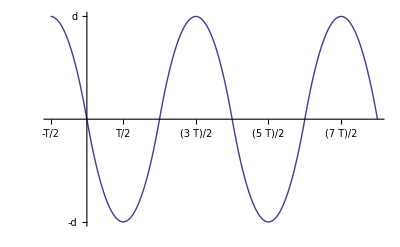

```mathematica
Plot[g[t],{t,-1/4,2},Ticks->{{{1/4,T/2},{1/2,T},{3/4,3T/2},{1,2T},{5/4,5T/2},{3/2,3T},{7/4,7T/2},{2,4T},{-1/4,-T/2}},{{1,d},{-1,-d}}},TicksStyle->Directive[18]]
```